```mathematica
(*
josl@josl-ubuntu:~/Documents/CARMEN-internal/trunk/dsl/catkin_ws$ svn info
Path: .Working Copy Root Path: /home/josl/Documents/CARMEN-internal
URL:https://aero.mmmi.sdu.dk/svn/CARMEN-internal/trunk/dsl/catkin_ws
Relative URL: ^/trunk/dsl/catkin_ws
Repository Root:https://aero.mmmi.sdu.dk/svn/CARMEN-internal
Repository UUID:290bb8a6-ef15-4619-b365-4bd173ac4f53
Revision:910
Node Kind:directory
Schedule:normal
Last Changed Author:jlaursen
Last Changed Rev:910
Last Changed Date:2016-07-28 16:21:35+0200 (Thu,28 Jul 2016)
*)
```

```mathematica
useUbuntu=False;
pathBase="C:\\Users\\josl\\Dropbox\\forceexperiments\\28-07-16 ICRA Example experiment\\";
If[useUbuntu,pathBase="/home/josl/Dropbox/forceexperiments/28-07-16 ICRA Example experiment/"];
pathFilesData={"base.txt","catch.txt","crash.txt"};
```

#### DataImport

```mathematica
dataImport[pathf_]:=Module[{res={},data},
For[qPath=1,qPath≤Length[pathf],qPath++,
path=pathBase <>pathf[[qPath]];
data =Take[Import[path,"Table","HeaderLines"->1],All ];
AppendTo[res,data];
];
Return[res]
];
data=dataImport[pathFilesData];
```

#### Data Structure

```mathematica
pathHeadings =pathBase <>pathFilesData[[1]];
Headings =Flatten[Take[Import[pathHeadings,"Table"],1]];

(* Variable heading assignments *)
iHeadings=Table["i"<>Headings[[i]],{i,Length[Headings]}];
Clear@@iHeadings;
lhs=ToExpression[iHeadings];
rhs=Table[i,{i,Length[Headings]}];
Inner[Set,lhs,rhs]; (*MapThread[(#1=#2)&,{lhs,rhs}]*)

(* Headings vissualisation *)
HeadingsSplit=StringSplit[Headings];
HeadingsList=Table[ToString[i]<>" = "<>HeadingsSplit[[i,1]],{i,1,Length[HeadingsSplit]}];
Partition[HeadingsList,7,7,1,{}][[1;;All,All]]//TableForm
(*Partition[HeadingsList,7,7,1,{}][[13,All]]//TableForm;*)

Print["Paths: " <> ToString[Length[ data ]]]
Print["Data points: " <> ToString[Length[ data[[1]] ]]]
Print["Collected elements: " <> ToString[Length[ data[[1]][[1]] ]]]
```

1 = force | 2 = force0 | 3 = force1 | 4 = force2 | 5 = force3 | 6 = force4 | 7 = force5
8 = dforce | 9 = dforce0 | 10 = dforce1 | 11 = dforce2 | 12 = dforce3 | 13 = dforce4 | 14 = dforce5
15 = TcpPose | 16 = TcpPose0 | 17 = TcpPose1 | 18 = TcpPose2 | 19 = TcpPose3 | 20 = TcpPose4 | 21 = TcpPose5
22 = dTcpPose | 23 = dTcpPose0 | 24 = dTcpPose1 | 25 = dTcpPose2 | 26 = dTcpPose3 | 27 = dTcpPose4 | 28 = dTcpPose5
29 = q | 30 = q0 | 31 = q1 | 32 = q2 | 33 = q3 | 34 = q4 | 35 = q5
36 = dq | 37 = dq0 | 38 = dq1 | 39 = dq2 | 40 = dq3 | 41 = dq4 | 42 = dq5
43 = iActual | 44 = iActual0 | 45 = iActual1 | 46 = iActual2 | 47 = iActual3 | 48 = iActual4 | 49 = iActual5
50 = iControl | 51 = iControl0 | 52 = iControl1 | 53 = iControl2 | 54 = iControl3 | 55 = iControl4 | 56 = iControl5
57 = sampleN | 58 = time | 59 = timeRelative | 60 = timePc | 61 = timePcRelative | 62 = safetyMode | 63 = errorState
64 = meanForce | 65 = meanForce0 | 66 = meanForce1 | 67 = meanForce2 | 68 = meanForce3 | 69 = meanForce4 | 70 = meanForce5
71 = medianForce | 72 = medianForce0 | 73 = medianForce1 | 74 = medianForce2 | 75 = medianForce3 | 76 = medianForce4 | 77 = medianForce5
78 = maxForce | 79 = maxForce0 | 80 = maxForce1 | 81 = maxForce2 | 82 = maxForce3 | 83 = maxForce4 | 84 = maxForce5
85 = minForce | 86 = minForce0 | 87 = minForce1 | 88 = minForce2 | 89 = minForce3 | 90 = minForce4 | 91 = minForce5
92 = stdDForce | 93 = stdDForce0 | 94 = stdDForce1 | 95 = stdDForce2 | 96 = stdDForce3 | 97 = stdDForce4 | 98 = stdDForce5
99 = varForce | 100 = varForce0 | 101 = varForce1 | 102 = varForce2 | 103 = varForce3 | 104 = varForce4 | 105 = varForce5
106 = meanCurrent | 107 = meanCurrent0 | 108 = meanCurrent1 | 109 = meanCurrent2 | 110 = meanCurrent3 | 111 = meanCurrent4 | 112 = meanCurrent5
113 = medianCurrent | 114 = medianCurrent0 | 115 = medianCurrent1 | 116 = medianCurrent2 | 117 = medianCurrent3 | 118 = medianCurrent4 | 119 = medianCurrent5
120 = maxCurrent | 121 = maxCurrent0 | 122 = maxCurrent1 | 123 = maxCurrent2 | 124 = maxCurrent3 | 125 = maxCurrent4 | 126 = maxCurrent5
127 = minCurrent | 128 = minCurrent0 | 129 = minCurrent1 | 130 = minCurrent2 | 131 = minCurrent3 | 132 = minCurrent4 | 133 = minCurrent5
134 = stdDCurrent | 135 = stdDCurrent0 | 136 = stdDCurrent1 | 137 = stdDCurrent2 | 138 = stdDCurrent3 | 139 = stdDCurrent4 | 140 = stdDCurrent5
141 = varCurrent | 142 = varCurrent0 | 143 = varCurrent1 | 144 = varCurrent2 | 145 = varCurrent3 | 146 = varCurrent4 | 147 = varCurrent5
148 = corrIndexSet0 | 149 = corrIndexPercentageSet0 | 150 = corrIndexQEndDistSet0 | 151 = datasetForce0Sample | 152 = datasetForce0Sample0 | 153 = datasetForce0Sample1 | 154 = datasetForce0Sample2
155 = datasetForce0Sample3 | 156 = datasetForce0Sample4 | 157 = datasetForce0Sample5 | 158 = datasetCurrent0Sample | 159 = datasetCurrent0Sample0 | 160 = datasetCurrent0Sample1 | 161 = datasetCurrent0Sample2
162 = datasetCurrent0Sample3 | 163 = datasetCurrent0Sample4 | 164 = datasetCurrent0Sample5 |  |  |  |

Paths: 3

Data points: 371

Collected elements: 164

#### Data Structure

```mathematica
getData[set_,range_,i_]:=data[[set,range,i]];
getData[set_,i_]:=data[[set,All,i]];
getData[i_]:=data[[All,All,i]];
getDataR[range_,i_]:=data[[All,range,i]];

getHeading[set_,i_]:=ToString[Headings[[i]]]<> " - "<>"set: "<> ToString[set] ;
getHeading[i_]:=Table[getHeading[set,i],{set,1,Length[data]}];

getLegned[set_,i_]:=PlotLegends->getHeading[set,i];
getLegend[i_]:=PlotLegends->getHeading[i];

myResample[list_]:=Table[ArrayResample[list[[i]],2000],{i,1,Length[list]}]
myRescale[list_]:=Join[Table[0,{u,0,50}],Rescale[list[[51;;All]]]]
myRescale[list_,offset_]:=myRescale[list]+offset
myRescale[list_,offset_,range_]:=myRescale[list]*range+offset
```

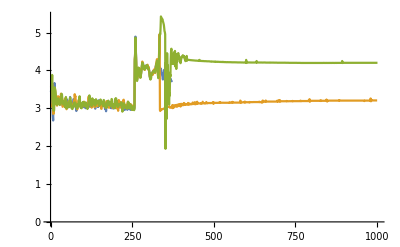
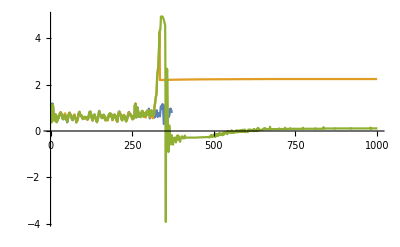
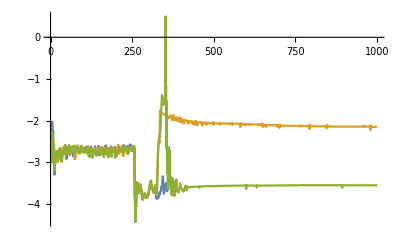
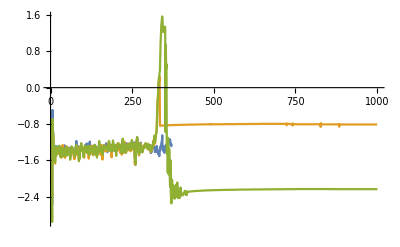
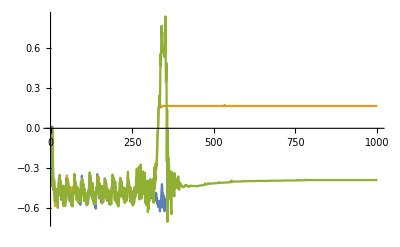
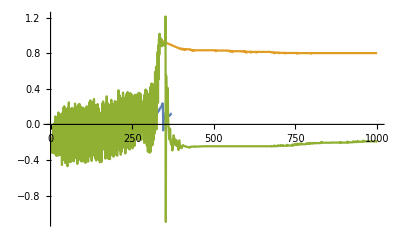
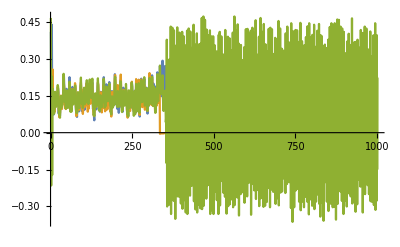

```mathematica
(* CURRENTS *)
plots=Table[{
dataF1=getData[All,iiControl+set];
p1=ListLinePlot[dataF1,PlotRange->Full]
},{set,0,6,1}]
```

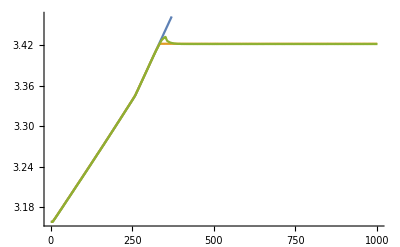
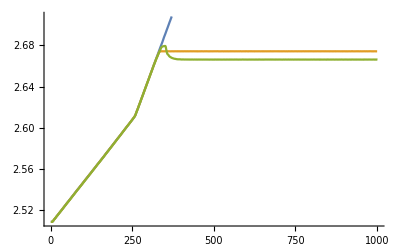
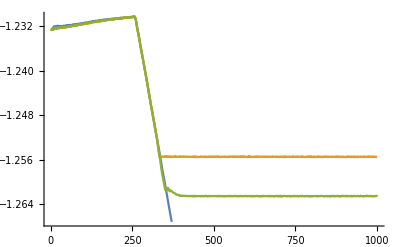
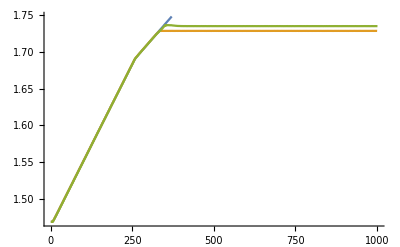
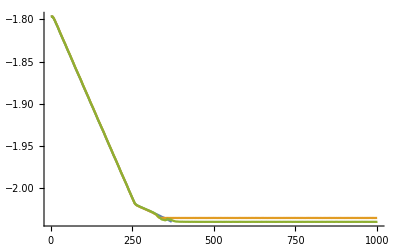
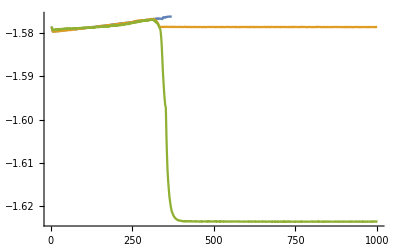
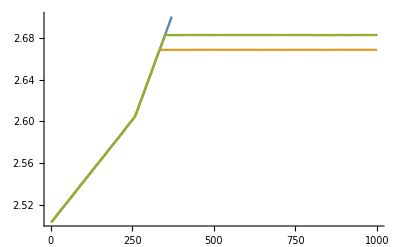

```mathematica
(* JONITVALUES *)
plots=Table[{
dataF1=getData[All,iq+set];
p1=ListLinePlot[dataF1,PlotRange->Full]
},{set,0,6,1}]
```

```mathematica
(* FORCE *)
plots=Table[{
dataF1=getData[All,iforce+set];
p1=ListLinePlot[dataF1,PlotRange->Full]
},{set,0,6,1}]
```

```mathematica
(* GLOBAL VARIANCE *)
(*stdGlobal=Table[StandardDeviation[getData[set,iiControl]],{set,1,20,1}];*)

(* ALL CURRENTS *)
allP=getData[All,iiControl];
p1=ListLinePlot[allP,PlotStyle->LightGray];
p2=ListPlot[allP,PlotStyle->Gray,PlotMarkers->"."];
```

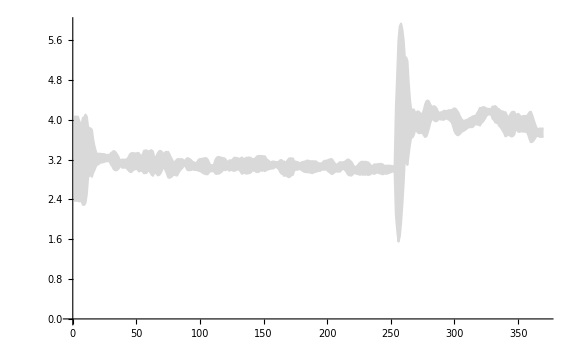

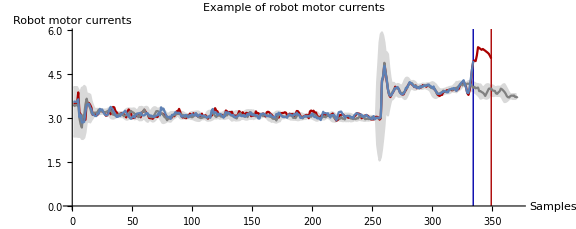

```mathematica
(* Graph example*)
set=1;
windowSize=7;
rangeStart=1;
type=iiControl;

samples=getData[set,rangeStart;;All,type];
stdV=MovingMap[StandardDeviation,samples,windowSize];
mean=MovingMap[Mean,samples,windowSize];
stdV=Join[Table[First[stdV],windowSize/2] , stdV,Table[Last[stdV],windowSize/2] ];
mean=Join[Table[First[mean],windowSize/2] , mean,Table[Last[mean],windowSize/2] ];

min =mean+2.5*stdV;
max =mean-2.5*stdV;

expectations=ListLinePlot[{max,min},Filling->{1->{2}},PlotStyle->LightGray,FillingStyle->LightGray,PlotRange->{{0,370-rangeStart},{2.5,3.5}}]
samples=ListLinePlot[samples,PlotStyle->Gray];

catchSample=getData[2,ierrorState];
catchSampleX=Position[catchSample,2][[1,1]];
catchLine=Graphics[{Darker[Blue],Thick,Line[{{catchSampleX-rangeStart,0},{catchSampleX-rangeStart,10}}]}];

crashSample=getData[3,isafetyMode];
crashSampleX=Position[crashSample,3][[1,1]];
crashLine=Graphics[{Darker[Red],Thick,Line[{{crashSampleX-rangeStart,0},{crashSampleX-rangeStart,10}}]}];

catch=ListLinePlot[getData[2,rangeStart;;catchSampleX-1,type],PlotRange->Full];
crash=ListLinePlot[getData[3,rangeStart;;crashSampleX-1,type],PlotStyle->Darker[Red],PlotRange->Full];

fontSizeSMP =11;
expectationsSMP=ListLinePlot[{max,min},Filling->{1->{2}},PlotStyle->LightGray,FillingStyle->LightGray,PlotRange->{{50,225-rangeStart},{1.5,6}}];
smallPlot=Show[expectationsSMP,catchLine,crashLine,crash,samples,catch,
AspectRatio->1/2.5,
AxesStyle->{fontSizeSMP,fontSizeSMP}];

fontSize =20;
Show[expectations,catchLine,crashLine,crash,samples,catch,
Epilog->Inset[smallPlot,{100,5},Automatic,150],
ImageSize->Large,
AxesLabel->{
Style["Samples",FontSize->fontSize],
Style["Robot motor\n currents",FontSize->fontSize]},
PlotLabel->Style["Example of robot motor currents",FontSize->fontSize+2],
AspectRatio->1/2.5,
AxesStyle->{fontSize,fontSize}]
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

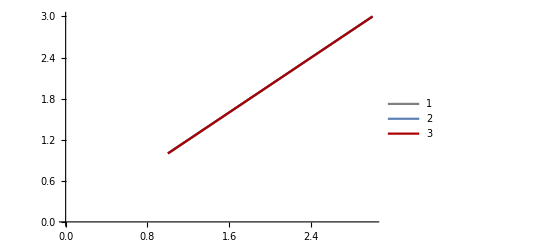

```mathematica
ListLinePlot[{{1,2,3},{1,2,3},{1,2,3}},PlotStyle->{Gray,ColorData[97,"ColorList"][[1]],Darker[Red]},PlotLegends->{Automatic}]
```